```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
c=Import["sol.txt","Data"];a=c[[1,1]];Ua=c[[1,2]];b=c[[Length[c],1]];Ub=c[[Length[c],2]];sol=NDSolve[{D[E^x D[u[x],x],x]==100Sin[10x],u[a]==Ua,u[b]==Ub},u,{x,a,b}];
```

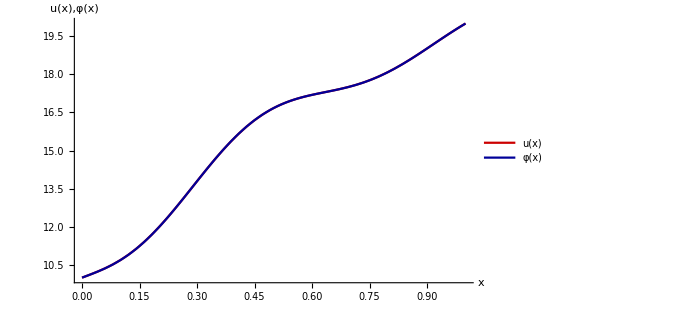

```mathematica
Show[Plot[u[x]/.sol,{x,0,1},LabelStyle->Directive[20],PlotStyle->{Darker[Red,0.2],Thick},PlotLegends->{"u(x)"}],ListLinePlot[c,LabelStyle->Directive[20],PlotLegends->{"φ(x)"},PlotStyle->{Darker[Blue,0.4],Thick}],AxesStyle->Thick,AxesLabel->{"x","u(x),φ(x)"},ImageSize->500,PlotRange->{c[[1,2]],c[[Length[c],2]]}]
```